## 18024563019 BSC (HONS.)MATHS Sixth Semester COMPLEX ANALYSIS PRACTICAL Practical EXAM 1.05.2021

## QUESTION 1

The given function f(z)=z Sin[z^2]

The Taylor series Expansion of f(z) around z=0is 
z^3-z^7/6

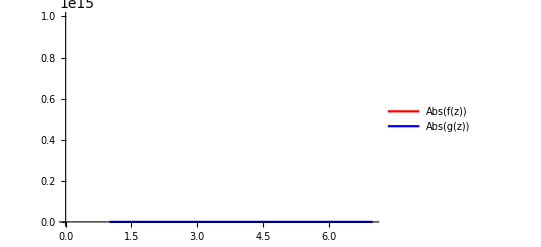

```mathematica
f[z_]=z* Sin[z^2];
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,10}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

## QUESTION 2

6+11 ⅈ

2-5 ⅈ

z1+z2 = 8+6 ⅈ

z1-z2 = 4+16 ⅈ

z1*z2 = 67-8 ⅈ

z1/z2 = -43/29+(52 ⅈ)/29

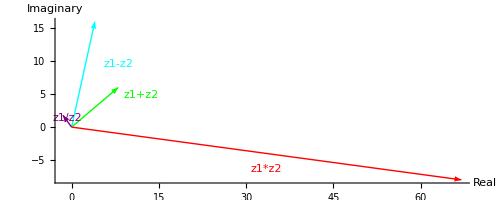

```mathematica
z1=6+11 I
z2=2-5 I
Print["z1+z2 = ",z1+z2]
Print["z1-z2 = ",z1-z2]
Print["z1*z2 = ",z1*z2]
Print["z1/z2 = ",z1/z2]
a=Graphics[{Green,Arrow[{{0,0},{Re[z1+z2],Im[z1+z2]}}],Text["z1+z2",{1.5 Re[z1+z2],0.8 Im[z1+z2]}]},Axes->True,AxesStyle->Arrowheads[{-0.04,0.04}],AxesLabel->{Real,Imaginary}];
b=Graphics[{Cyan,Arrow[{{0,0},{Re[z1-z2],Im[z1-z2]}}],Text["z1-z2",{2 Re[z1-z2],0.6 Im[z1-z2]}]},Axes->True,AxesStyle->Arrowheads[{-0.04,0.04}]];
c=Graphics[{Red,Arrow[{{0,0},{Re[z1*z2],Im[z1*z2]}}],Text["z1*z2",{Re[z1*z2]/2,0.8 Im[z1*z2]}]},Axes->True,AxesStyle->Arrowheads[{-0.04,0.04}]];
d=Graphics[{Purple,Arrow[{{0,0},{Re[z1/z2],Im[z1/z2]}}],Text["z1/z2",{Re[z1/z2]/2,0.8 Im[z1/z2]}]},Axes->True,AxesStyle->Arrowheads[{-0.04,0.04}]];
Show[a,b,c,d]
```

## QUESTION 3

## QUESTION 4

```mathematica
f[z_]:=(z^2-2 z)/((z+1)^2*(z^2+4));
s=z/.Solve[Denominator[f[z]]==0,z];
Print["Singularities are ",s];
For[i=1,i≤Length[s],i++,
res=Residue[f[z],{z,s[[i]]}];
Print["Residue at ",s[[i]]," is ",res]]
```

Singularities are {-1,-1,-2 ⅈ,2 ⅈ}

Residue at -1 is -14/25

Residue at -1 is -14/25

Residue at -2 ⅈ is 7/25-ⅈ/25

Residue at 2 ⅈ is 7/25+ⅈ/25

## QUESTION 5

x+ⅈ y

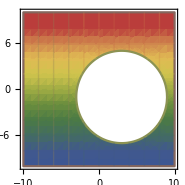

```mathematica
z=x+ⅈ y
RegionPlot[Abs[z-3+ⅈ]≥6,{x,-10,10},{y,-10,10},ColorFunction->"DarkRainbow",Mesh->9]
```

x+ⅈ y

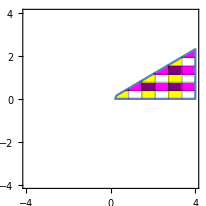

```mathematica
z=x+ⅈ y
RegionPlot[0≤Arg[z]≤π/6,{x,-4,4},{y,-4,4},MeshShading->{{Yellow,White},{Purple,Magenta}},Mesh->5]
```